```mathematica
Get["DiFfRG`"]
SetDirectory[GetDirectory[]]
```

Mathematica package DiFfRG loaded
Authors: Franz Richard Sattler
Version: 1.0
Year: 2024

Loading external packages

QMeS loaded

Mathematica package TensorBases loaded
Authors: Andreas Geißel, Franz Richard Sattler
Version: 1.0
Year: 2025

For a list of available bases, call TBInfo[]. For further information on a particular basis, call TBInfo["BasisName"].

This package provides the methods TBGetBasisElement, TBGetInnerProduct, TBGetMetric, TBGetInverseMetric, TBGetProjector for every tensor basis available.
For closer explanations, please call their usage messages, e.g. TBGetProjector::usage.

To build or manipulate bases, please call TBInfo["BaseBuilder"].

To show information on the used notation, call TBInfo["Notation"].

FormTracer package loaded.

To see all (user-defined and package-defined) FormTracer definitions, call TBInfo["FormTracer"].
Furthermore, TensorBases extends FormTracer. To see all extensions, call TBInfo["Extensions"]

Lorentz group undefined, using default names.

Group with name color undefined, using default names.

Group with name flavor undefined, using default names.

To see all momentum transformations that can be performed by TensorBases, call TBInfo["Momenta"].

TensorBases loaded

Flow output directory: /home/franz/Documents/Uni/Code/DiFfRG_main/DiFfRG/include/DiFfRG/physics/flows/

CodeTools loaded

/mnt/data/Documents/Uni/Code/DiFfRG_main/DiFfRG/include/DiFfRG/physics

# Polynomial

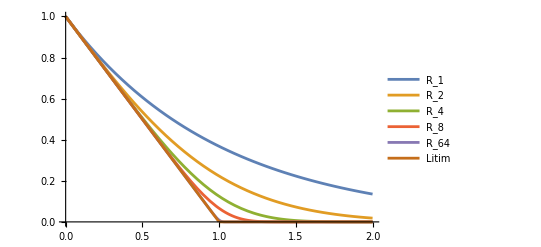

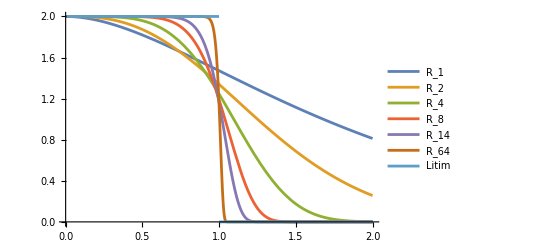

```mathematica
f[x_,n_]:=Total[Table[x^i/i,{i,1,n}]]
R[k_,x_,n_]:=k^2 Exp[-f[x,n]]
RLit[k_,x_]:=(k^2-k^2 x)HeavisideTheta[1-x]
DR[k_,p_,n_]:=D[R[ki,p2/ki^2,n],ki]ki//.ki->k//.p2->x k^2;
DRLit[k_,x_]=D[RLit[k,p2/k^2],k]k//.p2->x k^2;

Plot[Evaluate[Join[Map[R[1,x,#]&,{1,2,4,8,64}],{RLit[1,x]}]],{x,0,2},PlotLegends->Join[Map["R_"~~ToString[#]&,{1,2,4,8,64}],{"Litim"}]]
Plot[Evaluate[Join[Map[DR[1,x,#]&,{1,2,4,8,14,64}],{DRLit[1,x]}]],{x,0,2},PlotLegends->Join[Map["R_"~~ToString[#]&,{1,2,4,8,14,64}],{"Litim"}]]
```

```mathematica
out[expr_]:=Module[{str},
str=expr//FortranForm//ToString;
StringReplace[str,{"E**("->"np.exp("}]
];

DR[1,x,4]//out
DR[1,x,8]//out
DR[1,x,14]//out
DR[1,x,64]//out
```

2*np.exp(-x - x**2/2. - x**3/3. - x**4/4.) + np.exp(-x - x**2/2. - x**3/3. - x**4/4.)*(2*x + 2*x**2 + 2*x**3 + 2*x**4)

2*np.exp(-x - x**2/2. - x**3/3. - x**4/4. - x**5/5. - x**6/6. - x**7/7. - x**8/8.) + np.exp(-x - x**2/2. - x**3/3. - x**4/4. - x**5/5. - x**6/6. - x**7/7. - x**8/8.)*(2*x + 2*x**2 + 2*x**3 + 2*x**4 + 2*x**5 + 2*x**6 + 2*x**7 + 2*x**8)

2*np.exp(-x - x**2/2. - x**3/3. - x**4/4. - x**5/5. - x**6/6. - x**7/7. - x**8/8. - x**9/9. - x**10/10. - x**11/11. - x**12/12. - x**13/13. - x**14/14.) + np.exp(-x - x**2/2. - x**3/3. - x**4/4. - x**5/5. - x**6/6. - x**7/7. - x**8/8. - x**9/9. - x**10/10. - x**11/11. - x**12/12. - x**13/13. - x**14/14.)*(2*x + 2*x**2 + 2*x**3 + 2*x**4 + 2*x**5 + 2*x**6 + 2*x**7 + 2*x**8 + 2*x**9 + 2*x**10 + 2*x**11 + 2*x**12 + 2*x**13 + 2*x**14)

2*np.exp(-x - x**2/2. - x**3/3. - x**4/4. - x**5/5. - x**6/6. - x**7/7. - x**8/8. - x**9/9. - x**10/10. - x**11/11. - x**12/12. - x**13/13. - x**14/14. - x**15/15. - x**16/16. - x**17/17. - x**18/18. - x**19/19. - x**20/20. - x**21/21. - x**22/22. - x**23/23. - x**24/24. - x**25/25. - x**26/26. - x**27/27. - x**28/28. - x**29/29. - x**30/30. - x**31/31. - x**32/32. - x**33/33. - x**34/34. - x**35/35. - x**36/36. - x**37/37. - x**38/38. - x**39/39. - x**40/40. - x**41/41. - x**42/42. - x**43/43. - x**44/44. - x**45/45. - x**46/46. - x**47/47. - x**48/48. - x**49/49. - x**50/50. - x**51/51. - x**52/52. - x**53/53. - x**54/54. - x**55/55. - x**56/56. - x**57/57. - x**58/58. - x**59/59. - x**60/60. - x**61/61. - x**62/62. - x**63/63. - x**64/64.) + np.exp(-x - x**2/2. - x**3/3. - x**4/4. - x**5/5. - x**6/6. - x**7/7. - x**8/8. - x**9/9. - x**10/10. - x**11/11. - x**12/12. - x**13/13. - x**14/14. - x**15/15. - x**16/16. - x**17/17. - x**18/18. - x**19/19. - x**20/20. - x**21/21. - x**22/22. - x**23/23. - x**24/24. - x**25/25. - x**26/26. - x**27/27. - x**28/28. - x**29/29. - x**30/30. - x**31/31. - x**32/32. - x**33/33. - x**34/34. - x**35/35. - x**36/36. - x**37/37. - x**38/38. - x**39/39. - x**40/40. - x**41/41. - x**42/42. - x**43/43. - x**44/44. - x**45/45. - x**46/46. - x**47/47. - x**48/48. - x**49/49. - x**50/50. - x**51/51. - x**52/52. - x**53/53. - x**54/54. - x**55/55. - x**56/56. - x**57/57. - x**58/58. - x**59/59. - x**60/60. - x**61/61. - x**62/62. - x**63/63. - x**64/64.)*(2*x + 2*x**2 + 2*x**3 + 2*x**4 + 2*x**5 + 2*x**6 + 2*x**7 + 2*x**8 + 2*x**9 + 2*x**10 + 2*x**11 + 2*x**12 + 2*x**13 + 2*x**14 + 2*x**15 + 2*x**16 + 2*x**17 + 2*x**18 + 2*x**19 + 2*x**20 + 2*x**21 + 2*x**22 + 2*x**23 + 2*x**24 + 2*x**25 + 2*x**26 + 2*x**27 + 2*x**28 + 2*x**29 + 2*x**30 + 2*x**31 + 2*x**32 + 2*x**33 + 2*x**34 + 2*x**35 + 2*x**36 + 2*x**37 + 2*x**38 + 2*x**39 + 2*x**40 + 2*x**41 + 2*x**42 + 2*x**43 + 2*x**44 + 2*x**45 + 2*x**46 + 2*x**47 + 2*x**48 + 2*x**49 + 2*x**50 + 2*x**51 + 2*x**52 + 2*x**53 + 2*x**54 + 2*x**55 + 2*x**56 + 2*x**57 + 2*x**58 + 2*x**59 + 2*x**60 + 2*x**61 + 2*x**62 + 2*x**63 + 2*x**64)

out[2 ⅇ^(-x-x^2/2)+ⅇ^(-x-x^2/2) (2 x+2 x^2)]

# Rational

2 ⅇ^(-(x (-3 (2+9 x)+1.2 (6+27 x+14 x^2)))/(12 (-2+x) x+7.2 (1+4 x)+2 (-3+x^2)))+ⅇ^(-(x (-3 (2+9 x)+1.2 (6+27 x+14 x^2)))/(12 (-2+x) x+7.2 (1+4 x)+2 (-3+x^2))) (-(x (54 x+1.2 (-54 x-56 x^2)))/(12 (-2+x) x+7.2 (1+4 x)+2 (-3+x^2))+(x (-57.6 x-24 (-2+x) x-32 x^2) (-3 (2+9 x)+1.2 (6+27 x+14 x^2)))/(12 (-2+x) x+7.2 (1+4 x)+2 (-3+x^2))^2+(2 x (-3 (2+9 x)+1.2 (6+27 x+14 x^2)))/(12 (-2+x) x+7.2 (1+4 x)+2 (-3+x^2)))

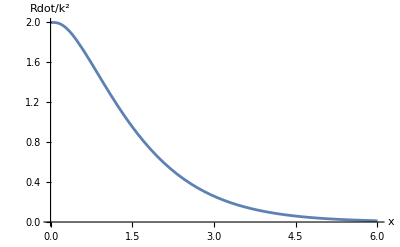

```mathematica
f[x_,n_]:=Total[Table[Symbol["a"~~ToString[i]] x^i,{i,1,n}]]/(1+b0 x^Quotient[n,2]+b1 x^(n-1))
Reg[x_,n_]:=Exp[-f[x,n]]
GetRational[n_]:=Module[{equations,symbols},
Clear[b0,b1,c];
equations=Join[
{Limit[D[Reg[x,n],{x,1}],x ->0]==-1},
Table[Limit[D[Reg[x,n],{x,i}],x->0]==0,{i,2,n}],
{Symbol["a"~~ToString[n]]/b1==c}
];
symbols=Join[
Table[Symbol["a"~~ToString[i]],{i,1,n}],
{b1}
];
Solve[
equations,
symbols
][[1]]
]
fun[n_]:=f[x,n]//.GetRational[n]//Simplify
dfun[n_]:=D[f[x,n],x]//.GetRational[n]//Simplify
toshow=k D[k^2 Exp[-fun[3]]//.x->p2/k^2,k]//.p2->x k^2//.k->1//.c->1.2//.b0->4
Plot[toshow,{x,0,6},AxesLabel->{x,Rdot/k^2}]
```

```mathematica
code="";
For[idx=1,idx<=16,idx++,
code=code~~"\nif constexpr(order == "~~ToString[idx]~~")\n  return "~~(fun[idx]//CodeForm)~~";";
]
code=code~~"\nstatic_assert(order <= "~~ToString[idx-1]~~", \"Rational regulator of order > "~~ToString[idx-1]~~" not implemented\");"
```

if constexpr(order == 1)
  return x;
if constexpr(order == 2)
  return x*(-2.+c*(2.+x+2.*b0*x))*powr<-1>(-2.+x+2.*c*(1.+b0*x));
if constexpr(order == 3)
  return x*(-3.*(2.+x+2.*b0*x)+c*(6.+(3.+6.*b0)*x+(2.+3.*b0)*powr<2>(x)))*powr<-1>(3.*b0*(-2.+x)*x+6.*c*(1.+b0*x)+2.*(-3.+powr<2>(x)));
if constexpr(order == 4)
  return 0.08333333333333333*x*(12.+6.*x+4.*(1.+3.*b0)*powr<2>(x)+3.*(c+2.*b0*c)*powr<-1>(-1.+c)*powr<3>(x))*powr<-1>(1.+b0*powr<2>(x)+0.25*(1.+2.*b0)*powr<-1>(-1.+c)*powr<3>(x));
if constexpr(order == 5)
  return 0.016666666666666666*x*(60.+30.*x+20.*(1.+3.*b0)*powr<2>(x)+15.*(1.+2.*b0)*powr<3>(x)+4.*(3.+5.*b0)*c*powr<-1>(-1.+c)*powr<4>(x))*powr<-1>(1.+b0*powr<2>(x)+0.06666666666666667*(3.+5.*b0)*powr<-1>(-1.+c)*powr<4>(x));
if constexpr(order == 6)
  return 0.016666666666666666*x*(60.+30.*x+20.*powr<2>(x)+15.*(1.+4.*b0)*powr<3>(x)+6.*(2.+5.*b0)*powr<4>(x)+10.*(c+2.*b0*c)*powr<-1>(-1.+c)*powr<5>(x))*powr<-1>(1.+b0*powr<3>(x)+0.16666666666666666*(1.+2.*b0)*powr<-1>(-1.+c)*powr<5>(x));
if constexpr(order == 7)
  return (x+0.5*powr<2>(x)+0.3333333333333333*powr<3>(x)+(0.25+b0)*powr<4>(x)+0.1*(2.+5.*b0)*powr<5>(x)+0.16666666666666666*(1.+2.*b0)*powr<6>(x)+0.03571428571428571*(4.+7.*b0)*c*powr<-1>(-1.+c)*powr<7>(x))*powr<-1>(1.+b0*powr<3>(x)+0.03571428571428571*(4.+7.*b0)*powr<-1>(-1.+c)*powr<6>(x));
if constexpr(order == 8)
  return (x+0.5*powr<2>(x)+0.3333333333333333*powr<3>(x)+0.25*powr<4>(x)+(0.2+b0)*powr<5>(x)+0.16666666666666666*(1.+3.*b0)*powr<6>(x)+0.047619047619047616*(3.+7.*b0)*powr<7>(x)+0.125*(1.+2.*b0)*c*powr<-1>(-1.+c)*powr<8>(x))*powr<-1>(1.+b0*powr<4>(x)+0.125*(1.+2.*b0)*powr<-1>(-1.+c)*powr<7>(x));
if constexpr(order == 9)
  return (x+0.5*powr<2>(x)+0.3333333333333333*powr<3>(x)+0.25*powr<4>(x)+(0.2+b0)*powr<5>(x)+0.16666666666666666*(1.+3.*b0)*powr<6>(x)+0.047619047619047616*(3.+7.*b0)*powr<7>(x)+0.125*(1.+2.*b0)*powr<8>(x)+0.022222222222222223*(5.+9.*b0)*c*powr<-1>(-1.+c)*powr<9>(x))*powr<-1>(1.+b0*powr<4>(x)+0.022222222222222223*(5.+9.*b0)*powr<-1>(-1.+c)*powr<8>(x));
if constexpr(order == 10)
  return (x+0.5*powr<2>(x)+0.3333333333333333*powr<3>(x)+0.25*powr<4>(x)+0.2*powr<5>(x)+(0.16666666666666666+b0)*powr<6>(x)+0.07142857142857142*(2.+7.*b0)*powr<7>(x)+0.041666666666666664*(3.+8.*b0)*powr<8>(x)+0.027777777777777776*(4.+9.*b0)*powr<9>(x)+0.1*(1.+2.*b0)*c*powr<-1>(-1.+c)*powr<10>(x))*powr<-1>(1.+b0*powr<5>(x)+0.1*(1.+2.*b0)*powr<-1>(-1.+c)*powr<9>(x));
if constexpr(order == 11)
  return (x+0.5*powr<2>(x)+0.3333333333333333*powr<3>(x)+0.25*powr<4>(x)+0.2*powr<5>(x)+(0.16666666666666666+b0)*powr<6>(x)+0.07142857142857142*(2.+7.*b0)*powr<7>(x)+0.041666666666666664*(3.+8.*b0)*powr<8>(x)+0.027777777777777776*(4.+9.*b0)*powr<9>(x)+0.1*(1.+2.*b0)*powr<10>(x)+0.015151515151515152*(6.+11.*b0)*c*powr<-1>(-1.+c)*powr<11>(x))*powr<-1>(1.+b0*powr<5>(x)+0.015151515151515152*(6.+11.*b0)*powr<-1>(-1.+c)*powr<10>(x));
if constexpr(order == 12)
  return (x+0.5*powr<2>(x)+0.3333333333333333*powr<3>(x)+0.25*powr<4>(x)+0.2*powr<5>(x)+0.16666666666666666*powr<6>(x)+(0.14285714285714285+b0)*powr<7>(x)+0.125*(1.+4.*b0)*powr<8>(x)+0.1111111111111111*(1.+3.*b0)*powr<9>(x)+0.05*(2.+5.*b0)*powr<10>(x)+0.01818181818181818*(5.+11.*b0)*powr<11>(x)+0.08333333333333333*(1.+2.*b0)*c*powr<-1>(-1.+c)*powr<12>(x))*powr<-1>(1.+b0*powr<6>(x)+0.08333333333333333*(1.+2.*b0)*powr<-1>(-1.+c)*powr<11>(x));
if constexpr(order == 13)
  return (x+0.5*powr<2>(x)+0.3333333333333333*powr<3>(x)+0.25*powr<4>(x)+0.2*powr<5>(x)+0.16666666666666666*powr<6>(x)+(0.14285714285714285+b0)*powr<7>(x)+0.125*(1.+4.*b0)*powr<8>(x)+0.1111111111111111*(1.+3.*b0)*powr<9>(x)+0.05*(2.+5.*b0)*powr<10>(x)+0.01818181818181818*(5.+11.*b0)*powr<11>(x)+0.08333333333333333*(1.+2.*b0)*powr<12>(x)+0.01098901098901099*(7.+13.*b0)*c*powr<-1>(-1.+c)*powr<13>(x))*powr<-1>(1.+b0*powr<6>(x)+0.01098901098901099*(7.+13.*b0)*powr<-1>(-1.+c)*powr<12>(x));
if constexpr(order == 14)
  return (x+0.5*powr<2>(x)+0.3333333333333333*powr<3>(x)+0.25*powr<4>(x)+0.2*powr<5>(x)+0.16666666666666666*powr<6>(x)+0.14285714285714285*powr<7>(x)+(0.125+b0)*powr<8>(x)+0.05555555555555555*(2.+9.*b0)*powr<9>(x)+0.03333333333333333*(3.+10.*b0)*powr<10>(x)+0.022727272727272728*(4.+11.*b0)*powr<11>(x)+0.016666666666666666*(5.+12.*b0)*powr<12>(x)+0.01282051282051282*(6.+13.*b0)*powr<13>(x)+0.07142857142857142*(1.+2.*b0)*c*powr<-1>(-1.+c)*powr<14>(x))*powr<-1>(1.+b0*powr<7>(x)+0.07142857142857142*(1.+2.*b0)*powr<-1>(-1.+c)*powr<13>(x));
if constexpr(order == 15)
  return (x+0.5*powr<2>(x)+0.3333333333333333*powr<3>(x)+0.25*powr<4>(x)+0.2*powr<5>(x)+0.16666666666666666*powr<6>(x)+0.14285714285714285*powr<7>(x)+(0.125+b0)*powr<8>(x)+0.05555555555555555*(2.+9.*b0)*powr<9>(x)+0.03333333333333333*(3.+10.*b0)*powr<10>(x)+0.022727272727272728*(4.+11.*b0)*powr<11>(x)+0.016666666666666666*(5.+12.*b0)*powr<12>(x)+0.01282051282051282*(6.+13.*b0)*powr<13>(x)+0.07142857142857142*(1.+2.*b0)*powr<14>(x)+0.008333333333333333*(8.+15.*b0)*c*powr<-1>(-1.+c)*powr<15>(x))*powr<-1>(1.+b0*powr<7>(x)+0.008333333333333333*(8.+15.*b0)*powr<-1>(-1.+c)*powr<14>(x));
if constexpr(order == 16)
  return (x+0.5*powr<2>(x)+0.3333333333333333*powr<3>(x)+0.25*powr<4>(x)+0.2*powr<5>(x)+0.16666666666666666*powr<6>(x)+0.14285714285714285*powr<7>(x)+0.125*powr<8>(x)+(0.1111111111111111+b0)*powr<9>(x)+0.1*(1.+5.*b0)*powr<10>(x)+0.030303030303030304*(3.+11.*b0)*powr<11>(x)+0.08333333333333333*(1.+3.*b0)*powr<12>(x)+0.015384615384615385*(5.+13.*b0)*powr<13>(x)+0.023809523809523808*(3.+7.*b0)*powr<14>(x)+(0.06666666666666667+0.14285714285714285*b0)*powr<15>(x)+0.0625*(1.+2.*b0)*c*powr<-1>(-1.+c)*powr<16>(x))*powr<-1>(1.+b0*powr<8>(x)+0.0625*(1.+2.*b0)*powr<-1>(-1.+c)*powr<15>(x));
static_assert(order <= 16, "Rational regulator of order > 16 not implemented");

```mathematica
code="";
For[idx=1,idx<=16,idx++,
code=code~~"\nif constexpr(order == "~~ToString[idx]~~")\n  return "~~(dfun[idx]//CodeForm)~~";";
]
code=code=code~~"\nstatic_assert(order <= "~~ToString[idx-1]~~", \"Rational regulator of order > "~~ToString[idx-1]~~" not implemented\");"
```

if constexpr(order == 1)
  return 1.;
if constexpr(order == 2)
  return (4.+c*(-8.-4.*(1.+2.*b0)*x+(1.+2.*b0)*powr<2>(x))+2.*powr<2>(c)*(2.+(2.+4.*b0)*x+b0*(1.+2.*b0)*powr<2>(x)))*powr<-2>(-2.+x+2.*c*(1.+b0*x));
if constexpr(order == 3)
  return (1.+x+2.*b0*x+0.3333333333333333*(-1.+3.*c+b0*(-3.+6.*c)+3.*(-1.+c)*powr<2>(b0))*powr<-1>(-1.+c)*powr<2>(x)+0.3333333333333333*b0*(2.+3.*b0)*c*powr<-1>(-1.+c)*powr<3>(x)+0.027777777777777776*c*powr<2>(2.+3.*b0)*powr<-2>(-1.+c)*powr<4>(x))*powr<-2>(1.+b0*x+0.16666666666666666*(2.+3.*b0)*powr<-1>(-1.+c)*powr<2>(x));
if constexpr(order == 4)
  return (1.+x+(1.+2.*b0)*powr<2>(x)+0.5*(1.+2.*b0)*(-1.+2.*c)*powr<-1>(-1.+c)*powr<3>(x)+0.041666666666666664*(-3.+2.*b0*(-7.+4.*c)+24.*(-1.+c)*powr<2>(b0))*powr<-1>(-1.+c)*powr<4>(x)+0.5*b0*(1.+2.*b0)*c*powr<-1>(-1.+c)*powr<5>(x)+0.0625*c*powr<2>(1.+2.*b0)*powr<-2>(-1.+c)*powr<6>(x))*powr<-2>(1.+b0*powr<2>(x)+0.25*(1.+2.*b0)*powr<-1>(-1.+c)*powr<3>(x));
if constexpr(order == 5)
  return ((1.+b0*powr<2>(x)+0.06666666666666667*(3.+5.*b0)*powr<-1>(-1.+c)*powr<4>(x))*(1.+x+(1.+3.*b0)*powr<2>(x)+(1.+2.*b0)*powr<3>(x)+0.3333333333333333*(3.+5.*b0)*c*powr<-1>(-1.+c)*powr<4>(x))-0.016666666666666666*x*(2.*b0*x+0.26666666666666666*(3.+5.*b0)*powr<-1>(-1.+c)*powr<3>(x))*(60.+30.*x+20.*(1.+3.*b0)*powr<2>(x)+15.*(1.+2.*b0)*powr<3>(x)+4.*(3.+5.*b0)*c*powr<-1>(-1.+c)*powr<4>(x)))*powr<-2>(1.+b0*powr<2>(x)+0.06666666666666667*(3.+5.*b0)*powr<-1>(-1.+c)*powr<4>(x));
if constexpr(order == 6)
  return ((1.+b0*powr<3>(x)+0.16666666666666666*(1.+2.*b0)*powr<-1>(-1.+c)*powr<5>(x))*(1.+x+powr<2>(x)+(1.+4.*b0)*powr<3>(x)+(1.+2.5*b0)*powr<4>(x)+(c+2.*b0*c)*powr<-1>(-1.+c)*powr<5>(x))-0.016666666666666666*x*(3.*b0*powr<2>(x)+0.8333333333333334*(1.+2.*b0)*powr<-1>(-1.+c)*powr<4>(x))*(60.+30.*x+20.*powr<2>(x)+15.*(1.+4.*b0)*powr<3>(x)+6.*(2.+5.*b0)*powr<4>(x)+10.*(c+2.*b0*c)*powr<-1>(-1.+c)*powr<5>(x)))*powr<-2>(1.+b0*powr<3>(x)+0.16666666666666666*(1.+2.*b0)*powr<-1>(-1.+c)*powr<5>(x));
if constexpr(order == 7)
  return ((1.+b0*powr<3>(x)+0.03571428571428571*(4.+7.*b0)*powr<-1>(-1.+c)*powr<6>(x))*(1.+x+powr<2>(x)+(1.+4.*b0)*powr<3>(x)+(1.+2.5*b0)*powr<4>(x)+(1.+2.*b0)*powr<5>(x)+0.25*(4.+7.*b0)*c*powr<-1>(-1.+c)*powr<6>(x))-1.*(3.*b0*powr<2>(x)+0.21428571428571427*(4.+7.*b0)*powr<-1>(-1.+c)*powr<5>(x))*(x+0.5*powr<2>(x)+0.3333333333333333*powr<3>(x)+(0.25+b0)*powr<4>(x)+0.1*(2.+5.*b0)*powr<5>(x)+0.16666666666666666*(1.+2.*b0)*powr<6>(x)+0.03571428571428571*(4.+7.*b0)*c*powr<-1>(-1.+c)*powr<7>(x)))*powr<-2>(1.+b0*powr<3>(x)+0.03571428571428571*(4.+7.*b0)*powr<-1>(-1.+c)*powr<6>(x));
if constexpr(order == 8)
  return ((1.+b0*powr<4>(x)+0.125*(1.+2.*b0)*powr<-1>(-1.+c)*powr<7>(x))*(1.+x+powr<2>(x)+powr<3>(x)+(1.+5.*b0)*powr<4>(x)+(1.+3.*b0)*powr<5>(x)+(1.+2.3333333333333335*b0)*powr<6>(x)+(c+2.*b0*c)*powr<-1>(-1.+c)*powr<7>(x))-1.*(4.*b0*powr<3>(x)+0.875*(1.+2.*b0)*powr<-1>(-1.+c)*powr<6>(x))*(x+0.5*powr<2>(x)+0.3333333333333333*powr<3>(x)+0.25*powr<4>(x)+(0.2+b0)*powr<5>(x)+0.16666666666666666*(1.+3.*b0)*powr<6>(x)+0.047619047619047616*(3.+7.*b0)*powr<7>(x)+0.125*(1.+2.*b0)*c*powr<-1>(-1.+c)*powr<8>(x)))*powr<-2>(1.+b0*powr<4>(x)+0.125*(1.+2.*b0)*powr<-1>(-1.+c)*powr<7>(x));
if constexpr(order == 9)
  return ((1.+b0*powr<4>(x)+0.022222222222222223*(5.+9.*b0)*powr<-1>(-1.+c)*powr<8>(x))*(1.+x+powr<2>(x)+powr<3>(x)+(1.+5.*b0)*powr<4>(x)+(1.+3.*b0)*powr<5>(x)+(1.+2.3333333333333335*b0)*powr<6>(x)+(1.+2.*b0)*powr<7>(x)+0.2*(5.+9.*b0)*c*powr<-1>(-1.+c)*powr<8>(x))-1.*(4.*b0*powr<3>(x)+0.17777777777777778*(5.+9.*b0)*powr<-1>(-1.+c)*powr<7>(x))*(x+0.5*powr<2>(x)+0.3333333333333333*powr<3>(x)+0.25*powr<4>(x)+(0.2+b0)*powr<5>(x)+0.16666666666666666*(1.+3.*b0)*powr<6>(x)+0.047619047619047616*(3.+7.*b0)*powr<7>(x)+0.125*(1.+2.*b0)*powr<8>(x)+0.022222222222222223*(5.+9.*b0)*c*powr<-1>(-1.+c)*powr<9>(x)))*powr<-2>(1.+b0*powr<4>(x)+0.022222222222222223*(5.+9.*b0)*powr<-1>(-1.+c)*powr<8>(x));
if constexpr(order == 10)
  return ((1.+b0*powr<5>(x)+0.1*(1.+2.*b0)*powr<-1>(-1.+c)*powr<9>(x))*(1.+x+powr<2>(x)+powr<3>(x)+powr<4>(x)+(1.+6.*b0)*powr<5>(x)+(1.+3.5*b0)*powr<6>(x)+(1.+2.6666666666666665*b0)*powr<7>(x)+(1.+2.25*b0)*powr<8>(x)+(c+2.*b0*c)*powr<-1>(-1.+c)*powr<9>(x))-1.*(5.*b0*powr<4>(x)+0.9*(1.+2.*b0)*powr<-1>(-1.+c)*powr<8>(x))*(x+0.5*powr<2>(x)+0.3333333333333333*powr<3>(x)+0.25*powr<4>(x)+0.2*powr<5>(x)+(0.16666666666666666+b0)*powr<6>(x)+0.07142857142857142*(2.+7.*b0)*powr<7>(x)+0.041666666666666664*(3.+8.*b0)*powr<8>(x)+0.027777777777777776*(4.+9.*b0)*powr<9>(x)+0.1*(1.+2.*b0)*c*powr<-1>(-1.+c)*powr<10>(x)))*powr<-2>(1.+b0*powr<5>(x)+0.1*(1.+2.*b0)*powr<-1>(-1.+c)*powr<9>(x));
if constexpr(order == 11)
  return ((1.+b0*powr<5>(x)+0.015151515151515152*(6.+11.*b0)*powr<-1>(-1.+c)*powr<10>(x))*(1.+x+powr<2>(x)+powr<3>(x)+powr<4>(x)+(1.+6.*b0)*powr<5>(x)+(1.+3.5*b0)*powr<6>(x)+(1.+2.6666666666666665*b0)*powr<7>(x)+(1.+2.25*b0)*powr<8>(x)+(1.+2.*b0)*powr<9>(x)+0.16666666666666666*(6.+11.*b0)*c*powr<-1>(-1.+c)*powr<10>(x))-1.*(5.*b0*powr<4>(x)+0.15151515151515152*(6.+11.*b0)*powr<-1>(-1.+c)*powr<9>(x))*(x+0.5*powr<2>(x)+0.3333333333333333*powr<3>(x)+0.25*powr<4>(x)+0.2*powr<5>(x)+(0.16666666666666666+b0)*powr<6>(x)+0.07142857142857142*(2.+7.*b0)*powr<7>(x)+0.041666666666666664*(3.+8.*b0)*powr<8>(x)+0.027777777777777776*(4.+9.*b0)*powr<9>(x)+0.1*(1.+2.*b0)*powr<10>(x)+0.015151515151515152*(6.+11.*b0)*c*powr<-1>(-1.+c)*powr<11>(x)))*powr<-2>(1.+b0*powr<5>(x)+0.015151515151515152*(6.+11.*b0)*powr<-1>(-1.+c)*powr<10>(x));
if constexpr(order == 12)
  return ((1.+b0*powr<6>(x)+0.08333333333333333*(1.+2.*b0)*powr<-1>(-1.+c)*powr<11>(x))*(1.+x+powr<2>(x)+powr<3>(x)+powr<4>(x)+powr<5>(x)+(1.+7.*b0)*powr<6>(x)+(1.+4.*b0)*powr<7>(x)+(1.+3.*b0)*powr<8>(x)+(1.+2.5*b0)*powr<9>(x)+(1.+2.2*b0)*powr<10>(x)+(c+2.*b0*c)*powr<-1>(-1.+c)*powr<11>(x))-1.*(6.*b0*powr<5>(x)+0.9166666666666666*(1.+2.*b0)*powr<-1>(-1.+c)*powr<10>(x))*(x+0.5*powr<2>(x)+0.3333333333333333*powr<3>(x)+0.25*powr<4>(x)+0.2*powr<5>(x)+0.16666666666666666*powr<6>(x)+(0.14285714285714285+b0)*powr<7>(x)+0.125*(1.+4.*b0)*powr<8>(x)+0.1111111111111111*(1.+3.*b0)*powr<9>(x)+0.05*(2.+5.*b0)*powr<10>(x)+0.01818181818181818*(5.+11.*b0)*powr<11>(x)+0.08333333333333333*(1.+2.*b0)*c*powr<-1>(-1.+c)*powr<12>(x)))*powr<-2>(1.+b0*powr<6>(x)+0.08333333333333333*(1.+2.*b0)*powr<-1>(-1.+c)*powr<11>(x));
if constexpr(order == 13)
  return ((1.+b0*powr<6>(x)+0.01098901098901099*(7.+13.*b0)*powr<-1>(-1.+c)*powr<12>(x))*(1.+x+powr<2>(x)+powr<3>(x)+powr<4>(x)+powr<5>(x)+(1.+7.*b0)*powr<6>(x)+(1.+4.*b0)*powr<7>(x)+(1.+3.*b0)*powr<8>(x)+(1.+2.5*b0)*powr<9>(x)+(1.+2.2*b0)*powr<10>(x)+(1.+2.*b0)*powr<11>(x)+0.14285714285714285*(7.+13.*b0)*c*powr<-1>(-1.+c)*powr<12>(x))-1.*(6.*b0*powr<5>(x)+0.13186813186813187*(7.+13.*b0)*powr<-1>(-1.+c)*powr<11>(x))*(x+0.5*powr<2>(x)+0.3333333333333333*powr<3>(x)+0.25*powr<4>(x)+0.2*powr<5>(x)+0.16666666666666666*powr<6>(x)+(0.14285714285714285+b0)*powr<7>(x)+0.125*(1.+4.*b0)*powr<8>(x)+0.1111111111111111*(1.+3.*b0)*powr<9>(x)+0.05*(2.+5.*b0)*powr<10>(x)+0.01818181818181818*(5.+11.*b0)*powr<11>(x)+0.08333333333333333*(1.+2.*b0)*powr<12>(x)+0.01098901098901099*(7.+13.*b0)*c*powr<-1>(-1.+c)*powr<13>(x)))*powr<-2>(1.+b0*powr<6>(x)+0.01098901098901099*(7.+13.*b0)*powr<-1>(-1.+c)*powr<12>(x));
if constexpr(order == 14)
  return ((1.+b0*powr<7>(x)+0.07142857142857142*(1.+2.*b0)*powr<-1>(-1.+c)*powr<13>(x))*(1.+x+powr<2>(x)+powr<3>(x)+powr<4>(x)+powr<5>(x)+powr<6>(x)+(1.+8.*b0)*powr<7>(x)+(1.+4.5*b0)*powr<8>(x)+(1.+3.3333333333333335*b0)*powr<9>(x)+(1.+2.75*b0)*powr<10>(x)+(1.+2.4*b0)*powr<11>(x)+(1.+2.1666666666666665*b0)*powr<12>(x)+(c+2.*b0*c)*powr<-1>(-1.+c)*powr<13>(x))-1.*(7.*b0*powr<6>(x)+0.9285714285714286*(1.+2.*b0)*powr<-1>(-1.+c)*powr<12>(x))*(x+0.5*powr<2>(x)+0.3333333333333333*powr<3>(x)+0.25*powr<4>(x)+0.2*powr<5>(x)+0.16666666666666666*powr<6>(x)+0.14285714285714285*powr<7>(x)+(0.125+b0)*powr<8>(x)+0.05555555555555555*(2.+9.*b0)*powr<9>(x)+0.03333333333333333*(3.+10.*b0)*powr<10>(x)+0.022727272727272728*(4.+11.*b0)*powr<11>(x)+0.016666666666666666*(5.+12.*b0)*powr<12>(x)+0.01282051282051282*(6.+13.*b0)*powr<13>(x)+0.07142857142857142*(1.+2.*b0)*c*powr<-1>(-1.+c)*powr<14>(x)))*powr<-2>(1.+b0*powr<7>(x)+0.07142857142857142*(1.+2.*b0)*powr<-1>(-1.+c)*powr<13>(x));
if constexpr(order == 15)
  return ((1.+b0*powr<7>(x)+0.008333333333333333*(8.+15.*b0)*powr<-1>(-1.+c)*powr<14>(x))*(1.+x+powr<2>(x)+powr<3>(x)+powr<4>(x)+powr<5>(x)+powr<6>(x)+(1.+8.*b0)*powr<7>(x)+(1.+4.5*b0)*powr<8>(x)+(1.+3.3333333333333335*b0)*powr<9>(x)+(1.+2.75*b0)*powr<10>(x)+(1.+2.4*b0)*powr<11>(x)+(1.+2.1666666666666665*b0)*powr<12>(x)+(1.+2.*b0)*powr<13>(x)+0.125*(8.+15.*b0)*c*powr<-1>(-1.+c)*powr<14>(x))-1.*(7.*b0*powr<6>(x)+0.11666666666666667*(8.+15.*b0)*powr<-1>(-1.+c)*powr<13>(x))*(x+0.5*powr<2>(x)+0.3333333333333333*powr<3>(x)+0.25*powr<4>(x)+0.2*powr<5>(x)+0.16666666666666666*powr<6>(x)+0.14285714285714285*powr<7>(x)+(0.125+b0)*powr<8>(x)+0.05555555555555555*(2.+9.*b0)*powr<9>(x)+0.03333333333333333*(3.+10.*b0)*powr<10>(x)+0.022727272727272728*(4.+11.*b0)*powr<11>(x)+0.016666666666666666*(5.+12.*b0)*powr<12>(x)+0.01282051282051282*(6.+13.*b0)*powr<13>(x)+0.07142857142857142*(1.+2.*b0)*powr<14>(x)+0.008333333333333333*(8.+15.*b0)*c*powr<-1>(-1.+c)*powr<15>(x)))*powr<-2>(1.+b0*powr<7>(x)+0.008333333333333333*(8.+15.*b0)*powr<-1>(-1.+c)*powr<14>(x));
if constexpr(order == 16)
  return ((1.+b0*powr<8>(x)+0.0625*(1.+2.*b0)*powr<-1>(-1.+c)*powr<15>(x))*(1.+x+powr<2>(x)+powr<3>(x)+powr<4>(x)+powr<5>(x)+powr<6>(x)+powr<7>(x)+(1.+9.*b0)*powr<8>(x)+(1.+5.*b0)*powr<9>(x)+(1.+3.6666666666666665*b0)*powr<10>(x)+(1.+3.*b0)*powr<11>(x)+(1.+2.6*b0)*powr<12>(x)+(1.+2.3333333333333335*b0)*powr<13>(x)+(1.+2.142857142857143*b0)*powr<14>(x)+(c+2.*b0*c)*powr<-1>(-1.+c)*powr<15>(x))-1.*(8.*b0*powr<7>(x)+0.9375*(1.+2.*b0)*powr<-1>(-1.+c)*powr<14>(x))*(x+0.5*powr<2>(x)+0.3333333333333333*powr<3>(x)+0.25*powr<4>(x)+0.2*powr<5>(x)+0.16666666666666666*powr<6>(x)+0.14285714285714285*powr<7>(x)+0.125*powr<8>(x)+(0.1111111111111111+b0)*powr<9>(x)+0.1*(1.+5.*b0)*powr<10>(x)+0.030303030303030304*(3.+11.*b0)*powr<11>(x)+0.08333333333333333*(1.+3.*b0)*powr<12>(x)+0.015384615384615385*(5.+13.*b0)*powr<13>(x)+0.023809523809523808*(3.+7.*b0)*powr<14>(x)+(0.06666666666666667+0.14285714285714285*b0)*powr<15>(x)+0.0625*(1.+2.*b0)*c*powr<-1>(-1.+c)*powr<16>(x)))*powr<-2>(1.+b0*powr<8>(x)+0.0625*(1.+2.*b0)*powr<-1>(-1.+c)*powr<15>(x));
static_assert(order <= 16, "Rational regulator of order > 16 not implemented");

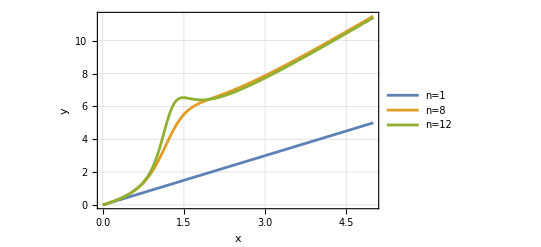

-Graphics-

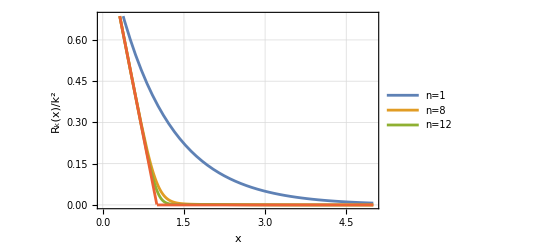

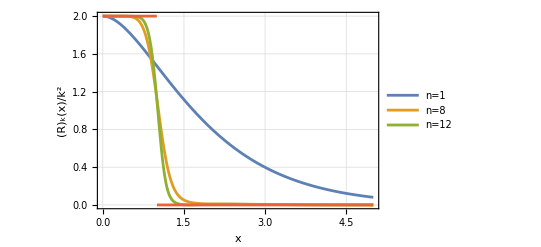

```mathematica
orders={1,8,12};
names={"n=1","n=8","n=12"};
cval=2;
b0val=0;

plotfs=Limit[Map[fun[#]&,orders],c->cval]//.b0->b0val;
Plot[plotfs,{x,0,5},PlotLegends->Placed[LineLegend[names],{Left,Top}],PlotLegends->orders,Frame->True,GridLines->Automatic,Axes->True,FrameLabel->{"x","y"},BaseStyle->{FontFamily->"Latin Modern Roman"}]

plotfs=Limit[Map[fun[#]&,orders],c->cval]//.b0->b0val;
Plot[plotfs,{x,0,5},PlotLegends->Placed[LineLegend[names],{Left,Top}],PlotLegends->orders,Frame->True,GridLines->Automatic,Axes->True,FrameLabel->{"x","y"},BaseStyle->{FontFamily->"Latin Modern Roman"}]

plotfs=Join[Limit[Map[Exp[-fun[#]]&,orders],c->cval]//.b0->b0val,{(1-x)HeavisideTheta[1-x]}];
Plot[plotfs,{x,0,5},PlotLegends->Placed[LineLegend[names],{Right,Top}],Frame->True,GridLines->Automatic,FrameLabel->{"x","R_k(x)/k^2"},BaseStyle->{FontFamily->"Latin Modern Roman"}]

plotdfs=Join[Limit[Map[k D[k^2 Exp[-fun[#]//.x->p^2/k^2],k]//.p->√x k//.k->1&,orders],c->cval]//.b0->b0val,{(2 k^2)HeavisideTheta[1-x]//.k->1}];
Plot[plotdfs,{x,0,5},PlotLegends->Placed[LineLegend[names],{Right,Top}],Frame->True,GridLines->Automatic,FrameLabel->{"x","(Ṙ)_k(x)/k^2"},BaseStyle->{FontFamily->"Latin Modern Roman"},LabelStyle->Medium]
```

```mathematica
things=ParallelMap[k D[k^2 Exp[-fun[#]//.x->p^2/k^2],k]//.c->2//.b0->0//.p->√x k//.k->1&,{4,8,14}];

out[expr_]:=Module[{str},
str=expr//FortranForm//ToString;
StringReplace[str,{"E**("->"np.exp("}]
];


things[[2]]//out

things=ParallelMap[k D[k^2 Exp[-fun[#]//.x->p^2/k^2],k]//.c->1.5//.b0->1//.p->√x k//.k->1&,{4,8,14}];

things[[2]]//out
```

2/np.exp((x + x**2/2. + x**3/3. + x**4/4. + x**5/5. + x**6/6. + x**7/7. + x**8/4.)/(1 + x**7/8.)) + (-((-2*x - 2*x**2 - 2*x**3 - 2*x**4 - 2*x**5 - 2*x**6 - 2*x**7 - 4*x**8)/(1 + x**7/8.)) - (7*x**7*(x + x**2/2. + x**3/3. + x**4/4. + x**5/5. + x**6/6. + x**7/7. + x**8/4.))/(4.*(1 + x**7/8.)**2))/np.exp((x + x**2/2. + x**3/3. + x**4/4. + x**5/5. + x**6/6. + x**7/7. + x**8/4.)/(1 + x**7/8.))

2/np.exp((x + x**2/2. + x**3/3. + x**4/4. + (6*x**5)/5. + (2*x**6)/3. + (10*x**7)/21. + 1.125*x**8)/(1 + x**4 + 0.75*x**7)) + (-((-2*x - 2*x**2 - 2*x**3 - 2*x**4 - 12*x**5 - 8*x**6 - (20*x**7)/3. - 18.*x**8)/(1 + x**4 + 0.75*x**7)) + ((-8*x**4 - 10.5*x**7)*(x + x**2/2. + x**3/3. + x**4/4. + (6*x**5)/5. + (2*x**6)/3. + (10*x**7)/21. + 1.125*x**8))/(1 + x**4 + 0.75*x**7)**2)/np.exp((x + x**2/2. + x**3/3. + x**4/4. + (6*x**5)/5. + (2*x**6)/3. + (10*x**7)/21. + 1.125*x**8)/(1 + x**4 + 0.75*x**7))